# Sphere Packing Ben Nissan and Tom Magerlein

## Packing Algorithm

## Distribute particles randomly on a sphere and set initial parameters

First we declare the number of particles we plan to pack.

```mathematica
numParticles = 12;
```

Next, we generate random coordinates (ranging from -1 to 1 on x, y, and z) for each particle and normalize them to fit to the unit sphere on which we are packing.  To do so, we generate a list of random unit vectors and set each one’s components as the coordinates of one of our points.

```mathematica
randUnitVec := Normalize[{2Random[] -1, 2Random[] - 1, 2Random[] - 1}];
```

```mathematica
xRand = Table[randUnitVec,{i,numParticles}];
```

```mathematica
x0 = Map[#/Norm[#]&,xRand];
```

We set the initial radius of each particle to some relatively small value—say, 0.01.

```mathematica
r0 = Table[0.01,{i,numParticles}];
```

Let’s visualize the particles to verify their random distribution on the sphere.

```mathematica
showParticles[x_,r_]:=Graphics3D[Join[{Green},Table[Sphere[x⟦i⟧,r⟦i⟧],{i,Length[x]}],{Gray,Sphere[{0,0,0}]}],Boxed->False];
```

```mathematica
showParticles[x0,r0]
```

-Graphics3D-

The particles appear to be randomly distributed, which is ideal.

## Moving along the sphere

Next, we create a function to randomly shift a particle along the surface of the sphere by some small amount.

```mathematica
shift[x_,δ_]:=Block[{dx,xNew,direction},

(* Generates a random magnitude and direction for our initial shift *)
direction=randUnitVec;
direction-=(direction.x) x/(x.x);
dx = RandomVariate[NormalDistribution[0,δ]] * Normalize[direction];

(* dx is currently in a completely random direction, which we need to fix so that our particle moves along the sphere's surface.  Because the local vector normal to the sphere at point x is parallel to vector x, we can subtract from dx the component parallel to vector x to force dx tangent to the sphere, a good first start. *)
dx-=(dx.x) x/(x.x);

(* Now, we shift x. *)
xNew = x + dx;

(* Finally, we reproject our new position onto the surface of the sphere and return the corrected position. *)
xNew /= Sqrt[xNew . xNew];

Return[xNew]
]
```

We can test this by running it multiple times on a point with arbitrary initial position and logging its movement over many iterations.  Ideally, this will produce a random path.

```mathematica
testx0 = {1,0,0};
randPath := Reap[Do[Sow[testx0=shift[testx0,0.03]],{i,1000}]];
Graphics3D[{Gray,Sphere[{0,0,0},1],Green,Line[randPath⟦2,1⟧]},Boxed-> False]
```

-Graphics3D-

And we see a nice random path.

## Shifting multiple particles

When moving multiple different particles along the same sphere, we need to make sure that none of them crash into each other or overlap.  We create a function to check, for each particle in a given list of coordinates, whether a desired shift is possible, shift the particle if so, and report whether the shift was successful.

```mathematica
checkAndShift[coords_,radii_,δ_,maxAttempts_]:=Block[{newCoords=coords,oldCoord,nearest,success=0,order,currentIdx},

(* For each particle in the list, selecting in random order: *)
order = RandomSample[Range[Length[coords]]];

Do[
(* We store our current position and generate a new one. *)
currentIdx = order⟦i⟧;
oldCoord=newCoords⟦currentIdx⟧;
newCoords⟦currentIdx⟧=shift[newCoords⟦currentIdx⟧,δ];

(* Then, we find the index of the nearest particle. *)
nearest=Last[Nearest[MapIndexed[#-> #2⟦1⟧&,newCoords],newCoords⟦currentIdx⟧,2]];

(* If the move results in a collision, we reject it. *)
Do[
	If[Norm[newCoords⟦currentIdx⟧-newCoords⟦nearest⟧]<radii⟦currentIdx⟧+radii⟦nearest⟧,
		newCoords⟦currentIdx⟧=oldCoord; 
		,
		success++;
		Break[];
	]
,{i,maxAttempts}];
(* And we iterate over the entire list. *)
,{i,Length[coords]}];

Return[{newCoords,success}]

]
```

Let’s test this on a fairly small list of fairly large particles over a large number of iterations.

```mathematica
testRadii = Table[0.4, {i, Length[x0]}];
testx0b = x0;
testPaths := Reap[Do[Sow[testx0b=checkAndShift[testx0b,testRadii,0.1,1]⟦1⟧],{i,100}]];
```

```mathematica
Graphics3D[Join[{Gray,Sphere[{0,0,0}]},Table[{Hue[i/Length[testx0b]],Line[Transpose[testPaths⟦2,1⟧]⟦i⟧]},{i,Length[testx0b]}]],Boxed-> False]
```

-Graphics3D-

## Packing the particles

Now that we can maneuver the particles around each other without collisions, we can pack!  We do so by writing a function that, over many iterations, does the following in each:
First, it calls checkAndShift on our list of particles, noting the ratio of successful moves to unsuccessful moves.  If the ratio is greater than zero, it inflates the particles by a small amount (much smaller than the distance we move them in checkAndShift) and proceds to the next iteration.  If the ratio is zero, then the particles are fully packed and the function exits.

We set our initial shift length and pack!

```mathematica
pack[r0_,x0_,δ0_,maxAttempts_]:=Block[{rCurrent = r0, xCurrent = x0, δCurrent = δ0,ratios,currentRatio},
ratios = Reap[Do[

(* Shifts the particles. *)
{xCurrent,currentRatio}=checkAndShift[xCurrent,rCurrent,δCurrent,maxAttempts];

(* Logs the number of moves accepted *)
Sow[currentRatio/Length[xCurrent]];

(* Stops if the acceptance ratio hits zero. *)
If[currentRatio==0,Break[]];

(* Inflates the particles otherwise. *)
rCurrent=Map[#+0.0005&,rCurrent];

,{i,2000}]];

Return[{ratios,xCurrent, rCurrent}]

]
```

We record our table of acceptance ratios, our final particle positions, and their final radii.

```mathematica
packResults = pack[r0,x0,.09,1];
ratioResults = packResults⟦1⟧;
xResults = packResults⟦2⟧;
rResults = packResults⟦3⟧;
```

We plot the acceptance ratios:

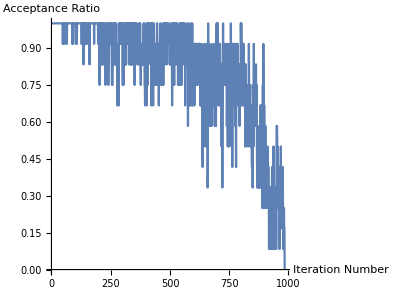

```mathematica
ListPlot[ratioResults⟦2,1⟧,Joined->True,AxesLabel->{"Iteration Number","Acceptance Ratio"},AspectRatio->3/4]
```

And, finally, show off our packed particles!

```mathematica
Show[showParticles[xResults,rResults],Boxed->False]
```

-Graphics3D-

## Adaptive Particle Inflation

```mathematica
findNearestPair[x0_]:=Block[{nearest,closestPair,closestDistSqr},
	nearest={};
	Do[
		AppendTo[nearest,Last[Nearest[MapIndexed[#-> #2⟦1⟧&,x0],x0⟦i⟧,2]]];
	,{i,Length[x0]}];
	closestPair={1,1};
	closestDistSqr=100;
	Do[
		If[Total[(x0⟦i⟧-x0⟦nearest⟦i⟧⟧)^2]<closestDistSqr,
			closestDistSqr=Total[(x0⟦i⟧-x0⟦nearest⟦i⟧⟧)^2];
			closestPair={i,nearest⟦i⟧};
		]
	,{i,Length[nearest]}];
	Return[{closestPair,Sqrt[closestDistSqr]}];
]
```

```mathematica
findNearestPair[x0]
```

{{5,11},0.12867}

```mathematica
adaptivePack[r0_,x0_,δ0_,maxAttempts_]:=Block[{rCurrent = r0, xCurrent = x0, δCurrent = δ0,ratios,currentRatio,nearest,inflation,inflationRatio},
ratios = Reap[Do[

nearest=findNearestPair[xCurrent];

inflation=Min[(nearest⟦2⟧-2rCurrent⟦1⟧)/4,.0005];
inflationRatio=inflation/0.0005;
If[inflation≤1*^-15,Break[]];

(* Inflate the particles *)
rCurrent=Map[#+inflation&,rCurrent];

(* Shifts the particles. *)
{xCurrent,currentRatio}=checkAndShift[xCurrent,rCurrent,δCurrent*Sqrt[inflationRatio],maxAttempts];

(* Logs the number of moves accepted *)
Sow[currentRatio/Length[xCurrent]];

(* Stops if the acceptance ratio hits zero. *)
If[currentRatio==0,Break[]];

,{i,2000}]];

Return[{ratios,xCurrent, rCurrent}]

]
```

```mathematica
adaptivePackResults = adaptivePack[r0,x0,.09,1];adaptiveRatioResults = adaptivePackResults⟦1⟧;
adaptiveXResults = adaptivePackResults⟦2⟧;
adaptiveRResults = adaptivePackResults⟦3⟧;
```

```mathematica
PackingFraction[adaptiveRResults]
```

0.790157

```mathematica
Show[showParticles[adaptiveXResults,adaptiveRResults],Boxed->False]
```

-Graphics3D-

```mathematica
-Graphics3D-.
```

## Data Collection

## Parameters

First, we have to set up various information about how what data we will be collecting: the number of runs we want to try for each configuration, the numbers of particles we will be packing, their initial radii, the amount we will be inflating them by at each iteration (or the maximum amount we will be inflating by for adaptive inflation), and the average amount we will be moving them by (again, the maximum if adaptive inflation is being used).

```mathematica
runsPerConfig=2;
particleCounts={12,20};
ri=.01;
δr0=.0005;
δx0=.09;
```

We also must set up our termination conditions, the number of consecutive iterations with a zero acceptance ratio that must occur before the algorithm terminates, or for adaptive inflation schemes potentially the minimum inflation that the algorithm will perform before it considers itself terminated:

```mathematica
maxAttemptCounts={2,5,10};
δrmin=.00005;
```

## Test Runs

Run all the configurations and collect data for them.  The data is broken down as follows:
- All data is stored within packOutputData
- Each element in packOutputData is a list corresponding to a specific run configuration
- The first element in this list the name of the configuration, as a string; the second is a list containing lists of the output from each run.
- The list corresponding to each run is the time that the run took, followed by the output from the packing output from that function.

```mathematica
Clear[packOutputData];
packOutputData={};
Do[
	Clear[configData];
	configData={};
	Do[
		x0= Table[randUnitVec,{particleCounts⟦particleCountIdx⟧}];
		r0 = Table[ri,{particleCounts⟦particleCountIdx⟧}];
		AppendTo[configData,Timing[pack[r0,x0,δx0,1]]];
	,{run,runsPerConfig}];
	AppendTo[packOutputData,{StringJoin["StandardPack-",ToString[particleCounts⟦particleCountIdx⟧],"particle"],configData}];
,{particleCountIdx,Length[particleCounts]}];
(*
Do[
Do[
	Clear[configData];
	configData={};
	Do[
		x0= Table[randUnitVec,{particleCounts⟦particleCountIdx⟧}];
		r0 = Table[ri,{particleCounts⟦particleCountIdx⟧}];
		AppendTo[configData,Timing[pack[r0,x0,δx0,maxAttemptCounts⟦attemptCountIdx⟧]]];
	,{run,runsPerConfig}]
	AppendTo[packOutputData,{StringJoin["ConvergenceCriterionPack-",ToString[maxAttemptCounts⟦attemptCountIdx⟧],"attempt-",ToString[particleCounts⟦particleCountIdx⟧],"particle"],configData}];
,{attemptCountIdx,Length[maxAttemptCounts]}];
,{particleCountIdx,Length[particleCounts]}];*)
Do[
	Clear[configData];
	configData={};
	Do[
		x0= Table[randUnitVec,{particleCounts⟦particleCountIdx⟧}];
		r0 = Table[ri,{particleCounts⟦particleCountIdx⟧}];
		AppendTo[configData,Timing[adaptivePack[r0,x0,δx0,1]]];
	,{run,runsPerConfig}];
	AppendTo[packOutputData,{StringJoin["AdaptivePack-",ToString[particleCounts⟦particleCountIdx⟧],"Particle-1Attempt"],configData}];
,{particleCountIdx,Length[particleCounts]}];
Do[
	Clear[configData];
	configData={};
	Do[
		x0= Table[randUnitVec,{particleCounts⟦particleCountIdx⟧}];
		r0 = Table[ri,{particleCounts⟦particleCountIdx⟧}];
		AppendTo[configData,Timing[adaptivePack[r0,x0,δx0,5]]];
	,{run,runsPerConfig}];
	AppendTo[packOutputData,{StringJoin["StandardPack-",ToString[particleCounts⟦particleCountIdx⟧],"Particle-5Attempt"],configData}];
,{particleCountIdx,Length[particleCounts]}];
```

## Testing multiple particles

We want to test the effect of packing different numbers of particles on the total number of iterations required for a full pack.  We set up a test with particles ranging from 2 (the minimum) to 30.  First, we initialize our relevant variables and set up a list to hold our results.

```mathematica
testNumParticles=Range[2,30];
testr0=.01;
testδ0=.03;
testRuns=5;
```

Next, we run the test, which will, for each number of particles, run the packing algorithm a given number of times, select the most-packed result (to account for randomness in the algorithm), and store the number of iterations it took that run to converge.

```mathematica
iterationList={};
Do[
	(*Our initial values.*)
	x0=Table[randUnitVec,{testNumParticles⟦i⟧}];
	r0=Table[testr0,{testNumParticles⟦i⟧}];
	(*The best packing fraction and pack that produced that fraction for the current number of particles.*)
	currentBestFraction=0;
	currentBestPack={};
	Do[
		(*Stores the current results.*)
		currentRun=pack[r0,x0,testδ0,1];
		(*Compares to the best run so far and substitutes it if better.*)
		If[PackingFraction[currentRun⟦3⟧]>currentBestFraction,
			currentBestFraction=PackingFraction[currentRun⟦3⟧];
			currentBestPack=currentRun];
	,{testRuns}];
	(*Appends the number of iterations for the best pack.*)
	 AppendTo[iterationList,Length[currentBestPack⟦1,2,1⟧]];
,{i,Length[testNumParticles]}];
```

```mathematica
iterationParticlePairList=Partition[Riffle[testNumParticles,iterationList],2]
```

{{2,1919},{3,1705},{4,1504},{5,1422},{6,1389},{7,1225},{8,1160},{9,1113},{10,1084},{11,1024},{12,1019},{13,923},{14,997},{15,870},{16,895},{17,832},{18,812},{19,794},{20,797},{21,794},{22,795},{23,763},{24,698},{25,727},{26,725},{27,782},{28,708},{29,706},{30,662}}

```mathematica
ListPlot[iterationList,AxesLabel->{"Number of Particles","Iterations to Converge"},PlotStyle->PointSize[Large],PlotRange->{500,1800}]
```

## Analysis

## Analysis Functions

First off, since our main figure of merit is the packing fraction (i.e. the fraction of the surface of the sphere being packed onto that is covered by the spheres that are being packed onto it) that each variation of the algorithm manages to obtain, we need to be able to find this quantity.

```mathematica
PackingFraction[radii_]:=Total[Map[Pi #^2&,radii]]/(4 Pi);
```

## Compute Run Statistics

In order to get any really meaningful data out of our runs, we have to compute various statistics for them.  The structure of the outputDataStats list is similar to that of packOutputData, above, except that instead of the list corresponding to each individual run containing a timing and then the output of the packing function, it contains the following, in order:
- The final packing fraction for the run
- The time it took for the run to complete
- The number of iterations it took for the algorithm to complete

```mathematica
Clear[outputDataStats];
outputDataStats={};
Do[
	Clear[configStats];
	configStats={};
	Do[
		runStats={PackingFraction[packOutputData⟦confIdx,2,runIdx,2,3⟧],packOutputData⟦confIdx,2,runIdx,1⟧,Length[packOutputData⟦confIdx,2,runIdx,2,1,2,1⟧]};
		(* Compute the packing fraction for the final packing and keep it as a statistic for the run *)
		(* Keep the total time for the run as a statistic *)
		(* Keep the total number of iterations for the run as a statistic *)
		AppendTo[configStats,runStats];
	,{runIdx,Length[packOutputData⟦confIdx,2⟧]}];
	AppendTo[outputDataStats,{packOutputData⟦confIdx,1⟧,configStats}];
,{confIdx,Length[packOutputData]}];
```

## Graph

Calculate the plot bounds, since Mathematica seems to have trouble setting them sensibly by default.

```mathematica
timeMax=Max[Table[
		Table[outputDataStats⟦confIdx,2,runIdx,2⟧
		,{runIdx,Length[outputDataStats⟦confIdx,2⟧]}]
		,{confIdx,Length[outputDataStats]}]];
iterMax=Max[Table[
		Table[outputDataStats⟦confIdx,2,runIdx,3⟧
		,{runIdx,Length[outputDataStats⟦confIdx,2⟧]}]
		,{confIdx,Length[outputDataStats]}]];
```

```mathematica
ratioVsTime=ListPlot[
		Table[
		Table[{outputDataStats⟦confIdx,2,runIdx,2⟧,outputDataStats⟦confIdx,2,runIdx,1⟧}
		,{runIdx,Length[outputDataStats⟦confIdx,2⟧]}]
		,{confIdx,Length[outputDataStats]}],
		PlotLegends->Table[outputDataStats⟦confIdx,1⟧,{confIdx,Length[outputDataStats]}],
		AxesLabel->{"Run Time (s)","Packing Ratio"},
		ImageSize->Large
];
```

```mathematica
ratioVsIters=ListPlot[
		Table[
		Table[{outputDataStats⟦confIdx,2,runIdx,3⟧,outputDataStats⟦confIdx,2,runIdx,1⟧}
		,{runIdx,Length[outputDataStats⟦confIdx,2⟧]}]
		,{confIdx,Length[outputDataStats]}],
		PlotLegends->Table[outputDataStats⟦confIdx,1⟧,{confIdx,Length[outputDataStats]}],
		AxesLabel->{"Iteration Count","Packing Ratio"},
		ImageSize->Large
];
```

```mathematica
timeVsIters=ListPlot[
		Table[
		Table[{outputDataStats⟦confIdx,2,runIdx,3⟧,outputDataStats⟦confIdx,2,runIdx,2⟧}
		,{runIdx,Length[outputDataStats⟦confIdx,2⟧]}]
		,{confIdx,Length[outputDataStats]}],
		PlotLegends->Table[outputDataStats⟦confIdx,1⟧,{confIdx,Length[outputDataStats]}],
		AxesLabel->{"Iteration Count","Run Time (s)"},
		ImageSize->Large
];
```

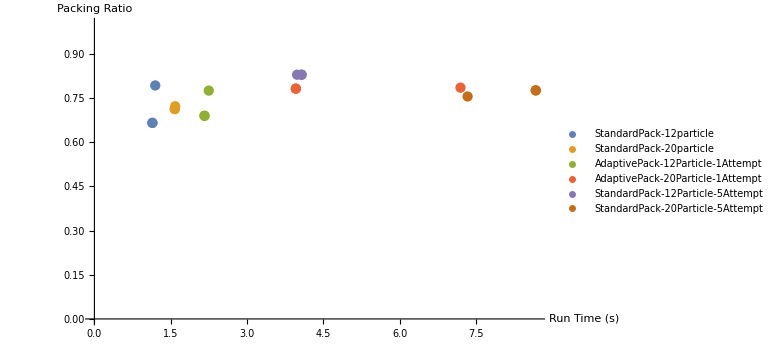

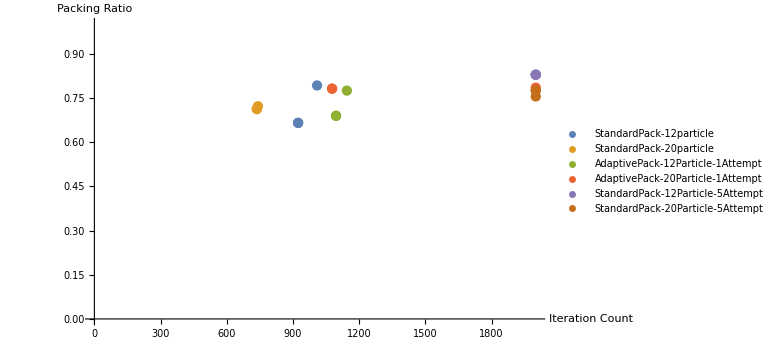

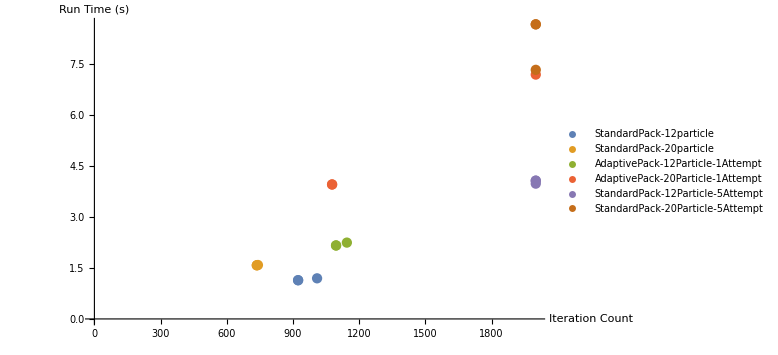

```mathematica
Show[ratioVsTime,PlotRange->{{0,timeMax},{0,1}},AxesOrigin->{0,0}]
Show[ratioVsIters,PlotRange->{{0,iterMax},{0,1}},AxesOrigin->{0,0}]
Show[timeVsIters,PlotRange->{{0,iterMax},{0,timeMax}},AxesOrigin->{0,0}]
```